```mathematica
Subscript[Ψ, nlm](r_,θ_,φ_)=√(2/π) ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l -l+n-12 l+1(2 r)/n Subscript[Y, l]^m(θ,φ)
```

(2^(3/2+l) ⅇ^(-r/n) (r/n)^l √(((-1-l+n)!)/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,φ])/(√π)

```mathematica
Subscript[n, ex(10)][r_]=Integrate[2*Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

```mathematica
Subscript[ñ, ex(10)][r_]=Subscript[n, ex(10)][r]*r^2
```

```mathematica
Subscript[n, TF(10)][r_]=((Sqrt[-0.164414+2/r])^3)*HeavisideTheta[-0.164414+2/r]/(3Pi^2)
```

```mathematica
Subscript[ñ, TF(10)][r_]=(4Pi r^2)*Subscript[n, TF(10)][r]
```

```mathematica
Subscript[n, 3(10)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(10)][r_]=(4Pi r^2)Subscript[n, 3(10)][r]
```

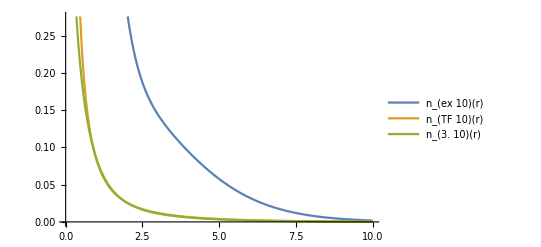

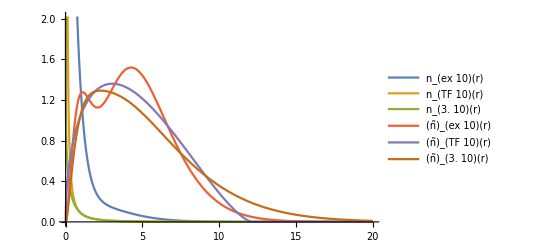

```mathematica
Plot[{Subscript[n, ex(10)][r],Subscript[n, TF(10)][r],Subscript[n, 3(10)][r]},{r,0,10},PlotLegends->"Expressions"]
Plot[{Subscript[n, ex(10)][r],Subscript[n, TF(10)][r],Subscript[n, 3(10)][r],Subscript[ñ, ex(10)][r],Subscript[ñ, TF(10)][r],Subscript[ñ, 3(10)][r]},{r,0,20},PlotLegends->"Expressions"]
```

```mathematica
Subscript[n, ex(2)][r_]=Integrate[2*Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,1},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

```mathematica
Subscript[ñ, ex(2)][r_]=Subscript[n, ex(2)][r]*r^2
```

```mathematica
Subscript[n, TF(2)][r_]=((Sqrt[-0.48075+2/r])^3)*HeavisideTheta[-0.48075+2/r]/(3Pi^2)
```

```mathematica
Subscript[ñ, TF(2)][r_]=(4Pi r^2)*Subscript[n, TF(2)][r]
```

```mathematica
Subscript[n, 3(2)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.48075)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(2)][r_]=(4Pi r^2)Subscript[n, 3(2)][r]
```

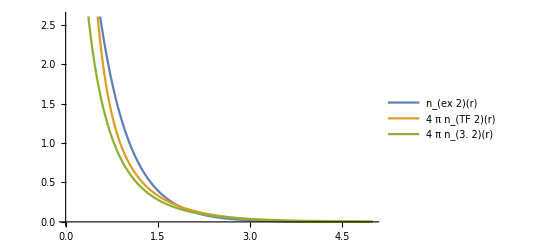

```mathematica
Plot[{Subscript[n, ex(2)][r],4Pi Subscript[n, TF(2)][r],4Pi Subscript[n, 3(2)][r]},{r,0,5},PlotLegends->"Expressions"]
```

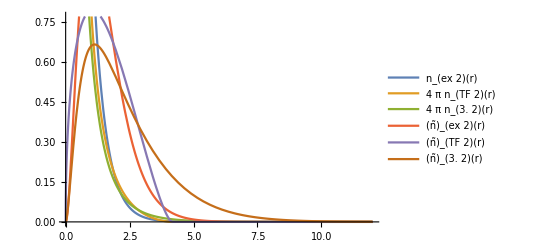

```mathematica
Plot[{Subscript[n, ex(2)][r],4Pi Subscript[n, TF(2)][r],4Pi Subscript[n, 3(2)][r],Subscript[ñ, ex(2)][r],Subscript[ñ, TF(2)][r],Subscript[ñ, 3(2)][r]},{r,0,12},PlotLegends->"Expressions"]
```

```mathematica
Subscript[n, ex(28)][r_]=Integrate[2*Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,3},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

```mathematica
Subscript[ñ, ex(28)][r_]=Subscript[n, ex(28)][r]*r^2
```

```mathematica
Subscript[n, TF(28)][r_]=((Sqrt[-0.0827625+2/r])^3)*HeavisideTheta[-0.0827625+2/r]/(3Pi^2)
```

```mathematica
Subscript[ñ, TF(28)][r_]=(4Pi r^2)Subscript[n, TF(28)][r]
```

```mathematica
Subscript[n, 3(28)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.0827625)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.0827625+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(28)][r_]=(4Pi r^2)Subscript[n, 3(28)][r]
```

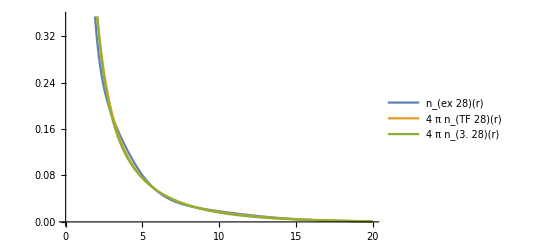

```mathematica
Plot[{Subscript[n, ex(28)][r],4Pi Subscript[n, TF(28)][r],4Pi Subscript[n, 3(28)][r]},{r,0,20},PlotLegends->"Expressions"]
```

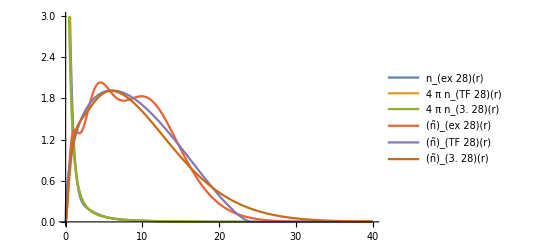

```mathematica
Plot[{Subscript[n, ex(28)][r],4Pi Subscript[n, TF(28)][r],4Pi Subscript[n, 3(28)][r],Subscript[ñ, ex(28)][r],Subscript[ñ, TF(28)][r],Subscript[ñ, 3(28)][r]},{r,0,40},PlotLegends->"Expressions"]
```

```mathematica
Subscript[n, ex(110)][r_]=Integrate[2*Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

```mathematica
Subscript[ñ, ex(110)][r_]=Subscript[n, ex(110)][r]*r^2
```

```mathematica
Subscript[n, TF(110)][r_]=((Sqrt[-0.03324125+2/r])^3)*HeavisideTheta[-0.03324125+2/r]/(3Pi^2)
```

```mathematica
Subscript[ñ, TF(110)][r_]=(4Pi r^2)*Subscript[n, TF(110)][r]
```

```mathematica
Subscript[n, 3(110)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.03324125)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.03324125+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.03324125+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(110)][r_]=(4Pi r^2)*Subscript[n, 3(110)][r]
```

```mathematica
Parallelize[Plot[{Subscript[n, ex(110)][r],4Pi Subscript[n, TF(110)][r],4Pi Subscript[n, 3(110)][r]},{r,0,40},PlotLegends->"Expressions"]]
```

```mathematica
Parallelize[Plot[{Subscript[n, ex(110)][r],4Pi Subscript[n, TF(110)][r],4Pi Subscript[n, 3(110)][r],Subscript[ñ, ex(110)][r],Subscript[ñ, TF(110)][r],Subscript[ñ, 3(110)][r]},{r,0,80},PlotLegends->"Expressions"]]
```

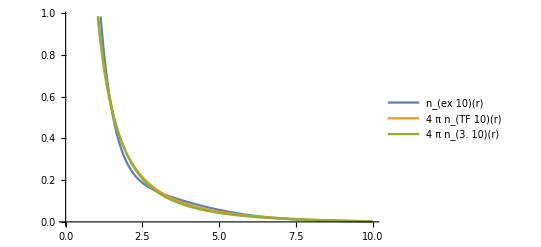

```mathematica
Plot[{Subscript[n, ex(10)][r],4Pi Subscript[n, TF(10)][r],4Pi Subscript[n, 3(10)][r]},{r,0,10},PlotLegends->"Expressions"]
```

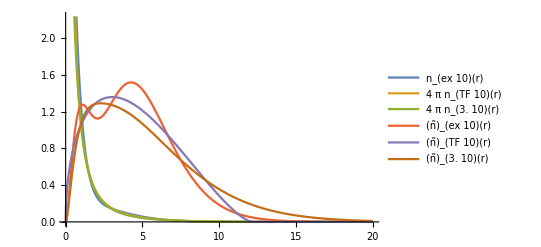

```mathematica
Plot[{Subscript[n, ex(10)][r],4Pi Subscript[n, TF(10)][r],4Pi Subscript[n, 3(10)][r],Subscript[ñ, ex(10)][r],Subscript[ñ, TF(10)][r],Subscript[ñ, 3(10)][r]},{r,0,20},PlotLegends->"Expressions"]
```

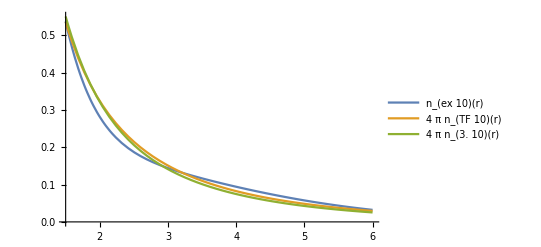

```mathematica
Plot[{Subscript[n, ex(10)][r],4Pi Subscript[n, TF(10)][r],4Pi Subscript[n, 3(10)][r]},{r,1.5,6},PlotLegends->"Expressions"]
```